# Discrete-time Quantum Walks (PoC)

## Definitions

## DTQW Environment

```mathematica
$DTQWEnvIcon=Graphics[{
Thick,
Circle[],
PointSize[Large],
Point[{0,0}]
},
ImageSize->Dynamic[{
Automatic,
3.5 CurrentValue["FontCapHeight"]/AbsoluteCurrentValue[Magnification]
}]
];
```

```mathematica
DTQWEnvAscQ[asc_?AssociationQ]:=And[
AllTrue[{"Type","Decoherent"},KeyExistsQ[asc,#]&],
Or[KeyExistsQ[asc,"Unitary"],AllTrue[{"Shift","Coin"},KeyExistsQ[asc,#]&]],
Xnor[asc["Decoherent"],AllTrue[{"Kraus","Probabilities"},KeyExistsQ[asc,#]&]],
Xnor[asc["Type"]=="FixedSize",KeyExistsQ[asc,"Size"]]
]
```

```mathematica
DTQWEnv[asc_?DTQWEnvAscQ]:=Module[{shift,coin,unit},
shift=asc["Shift"];
coin=asc["Coin"];
unit=Function[n,shift[n].coin[n]];
DTQWEnv[Append[asc,"Unitary"->unit]]
]/;Not[KeyExistsQ[asc,"Unitary"]]
```

```mathematica
DTQWEnv/:MakeBoxes[obj:DTQWEnv[asc_?DTQWEnvAscQ],form:(StandardForm|TraditionalForm)]:=
Module[{above,below},
above={
{BoxForm`SummaryItem[{"Type: ",asc["Type"]}],SpanFromLeft},
{BoxForm`SummaryItem[{"Decoherent: ",asc["Decoherent"]}],BoxForm`SummaryItem[{"Size: ",If[KeyExistsQ[asc,"Size"],asc["Size"],{∞,2}]}]}
};
below={
{BoxForm`SummaryItem[{"Information: ","This object represents a 1-dimensional discrete-time quantum walk with a two-dimensional coin"}],SpanFromLeft}
};
BoxForm`ArrangeSummaryBox[
DTQWEnv,
obj,
$DTQWEnvIcon,
above,
below,
form,
"Interpretable"->Automatic
]
];
```

## DTQW step

```mathematica
DTQWStep[rho_,DTQWEnv[env_],dim_]:=Chop[#.ArrayPad[rho,{{0,2},{0,2}}].ConjugateTranspose[#]]&[env["Unitary"][dim+1]]/;Not[env["Decoherent"]]
DTQWStep[rho_,DTQWEnv[env_]]:=Chop[#.ArrayPad[rho,{{0,2},{0,2}}].ConjugateTranspose[#]]&[env["Unitary"][Length[rho]/2+1]]/;Not[env["Decoherent"]]
DTQWStep[rho_,DTQWEnv[env_],dim_]:=With[{state=(#.ArrayPad[rho,{{0,2},{0,2}}].ConjugateTranspose[#])&[env["Unitary"][dim+1]]},
Inner[Chop[#1*#2[dim+1].state.ConjugateTranspose[#2[dim+1]]]&,env["Probabilities"],env["Kraus"],Plus]
]
DTQWStep[rho_,DTQWEnv[env_]]:=With[{state=(#.ArrayPad[rho,{{0,2},{0,2}}].ConjugateTranspose[#])&[env["Unitary"][Length[rho]/2+1]]},
Inner[Chop[#1*#2[Length[rho]/2+1].state.ConjugateTranspose[#2[Length[rho]/2+1]]]&,env["Probabilities"],env["Kraus"],Plus]
]
```

## DTQW

```mathematica
DTQW[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Do[ρ=DTQWStep[ρ,env,t],{t,n}];
ρ
]
```

## DTQW Trace

```mathematica
DTQWTrace[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Table[ρ=DTQWStep[ρ,env,t],{t,n}]
]
```

## Misc. functions

```mathematica
DTQWPosDistribution[rho_]:=Total/@Partition[Diagonal@rho,2]
```

```mathematica
DTQWPosExpvalue[prob_]:=Range[Length[#]].#&[prob]
```

```mathematica
DTQWPosStandardev[prob_]:=Sqrt[(Range[Length[#]]^2).#-DTQWPosExpvalue[#]^2]&[prob]
```

```mathematica
DTQWSdAdjustments[stdev_]:=Module[{lm,nlm},
lm=LinearModelFit[stdev,x,x];
nlm=NonlinearModelFit[stdev,A*Sqrt[x],{A},x];
If[lm["AdjustedRSquared"]<nlm["AdjustedRSquared"],
nlm,
lm
]
]
```

## Examples

## Operadores

```mathematica
α=π/6.;
```

```mathematica
CoinOperator[n_]:=SparseArray[Band[{1,1},{#,#}]->{{{Cos[α],Sin[α]},{-Sin[α],Cos[α]}}}]&[2n]
```

```mathematica
ShiftOperator[n_]:=SparseArray[Join[Table[{i,i},{i,Range[2,#,2]}],Table[{i,i-2},{i,Range[3,#,2]}]]->1,{#,#}]&[2*n]
```

```mathematica
UnitaryOperator[n_]:=ShiftOperator[n].CoinOperator[n]
```

```mathematica
FuzzyOperator[n_]:=RotateRight[IdentityMatrix[2*n,SparseArray],2]
```

## Examples

### Classic random walk

```mathematica
probs=N[Binomial[#,Range[0,#]]/2^#]&/@Range[0,100];
expvals=DTQWPosExpvalue/@probs;
sds=DTQWPosStandardev/@probs;
```

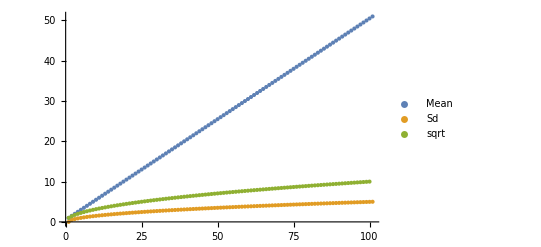

```mathematica
ListPlot[{expvals,sds,Sqrt[Range[100]]},
PlotLegends->{"Mean","Sd","sqrt"},
PlotRange->All
]
```

```mathematica
{#,#["AdjustedRSquared"]}&@NonlinearModelFit[sds,A*Sqrt[x]+B,{A,B},x]
```

{FittedModel[-0.148925+0.514697 √x],0.999864}

```mathematica
{#,#["AdjustedRSquared"]}&@NonlinearModelFit[sds,A*Sqrt[x]+B,{A,B},x,ConfidenceLevel->0.99]
```

{FittedModel[-0.148925+0.514697 √x],0.999864}

```mathematica
{#,#["AdjustedRSquared"]}&@LinearModelFit[sds,Sqrt[x],x]
```

{FittedModel[-0.148925+0.514697 √x],0.998838}

```mathematica
{#,#["AdjustedRSquared"]}&@LinearModelFit[sds,Sqrt[x],x,ConfidenceLevel->0.99]
```

{FittedModel[-0.148925+0.514697 √x],0.998838}